### Categorization

Tutorial

xTras

xTras`

xTras/tutorial/SymmetrizedDerivatives

### Keywords

Details

# Symmetrized Covariant Derivatives

## Introduction

A symmetrized derivative covariant derivative is symmetrization of a number of covariant derivatives:

∇_(a_1... a_n) = ∇_((a_1) ∇_a_2... ∇_(a_(n-1)) ∇_(a_n)) .

The main advantage of symmetrized derivatives is that they have a greater degree of symmetry than non-symmetrized (or ordinary) derivatives. For instance, it is obvious that the following is zero:

F^[ab]∇_(ab) T^c= 0 .

However, when we write out the symmetrized derivative, it is not immediately clear that the expression is zero:

F^[ab]∇_(ab) T^c=F^[ab] (∇_a ∇_b T^c+1/2 R_abd^c T^d)

Of course, when we write F^[ab] ∇_a ∇_b as a commutator, we recover zero. But the point is that eliminating commutators is something the xTensor canonicalizer does not do. So it is often necessary to explicitly symmetrize covariant derivatives in order to fully canonicalize an expression.

## Implementation

SymmetrizeCovDs | symmetrizes covariant derivatives
ExpandSymCovDs | de-symmetrizes covariant derivatives
$AutoSymmetrizeCovDs | when set to True, derivatives are automatically symmetrized

Functions for symmetrizing and de-symmetrizing covariant derivatives.

Symmetrized covariant derivatives are implement in xTras as follows. Whenever a covariant derivative CD is defined to be symmetrizable, CD[-a,-b] will mean ∇_(ab)  (and likewise for more indices). A covariant derivative can be defined to symmetrizable by giving the option SymCovDQ -> True  to DefCovD or DefMetric:

First define a manifold.

```mathematica
DefManifold[M,dim,IndexRange[a,l]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

Now define a metric and covariant derivative. We need to specify SymCovDQ in order to make the covariant derivative symmetrizable.

```mathematica
DefMetric[-1,metric[-a,-b],CD,PrintAs->"g",SymCovDQ->True]
```

** DefTensor: Defining symmetric metric tensor metric[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonmetric[-a,-b].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim d

** DefCovD:  Computing RicciToTFRicci for dim d

** DefCovD:  Computing RicciToEinsteinRules for dim d

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefCovD: Defining covariant derivative CD[-a]. to be symmetrizable

** DefTensor: Defining weight +2 density Detmetric[]. Determinant.

** DefParameter: Defining parameter PerturbationParametermetric.

** DefTensor: Defining tensor Perturbationmetric[LI[order],-a,-b].

And indeed, derivatives with more than one index are now interpreted as symmerized derivatives:

```mathematica
CD[-a,-b]@RicciScalarCD[]
```

▽_(ab)^R[▽]

We can expand the symmetrized derivative with a call to ExpandSymCovDs:

```mathematica
% // ExpandSymCovDs
```

1/2 (▽_a▽_b R[▽]+▽_b▽_a R[▽])

Ordinary derivatives can be symmetrized with SymmetrizeCovDs:

```mathematica
%//SymmetrizeCovDs//ToCanonical
```

▽_(ab)^R[▽]

Symmetrized derivatives are automatically Leibnitz:

```mathematica
CD[-a,-b][RicciScalarCD[]^2]
```

2 (▽_a R[▽]) (▽_b R[▽])+2 R[▽] (▽_(ab)^R[▽])

```mathematica
CD[-a,-b,-c][RicciScalarCD[]^2]
```

2 (▽_c R[▽]) (▽_(ab)^R[▽])+2 (▽_b R[▽]) (▽_(ac)^R[▽])+2 (▽_a R[▽]) (▽_(bc)^R[▽])+2 R[▽] (▽_(abc)^R[▽])

Integrating by parts can be done with VarD:

```mathematica
VarD[RicciScalarCD[], CD][ CD[a,b]@RicciScalarCD[] CD[-a,-b]@RicciScalarCD[] ] //ToCanonical
```

2 (▽_(ab)^▽_^(ab)R[▽])

Notice that two symmetrized derivatives acting on each other are not automatically symmetrized further. We need to call SymmetrizeCovDs again to do so explicitly:

```mathematica
%//SymmetrizeCovDs
```

2 (1/3 (▽^a R[▽]) (▽_b R[▽] |   | b
a |  )+1/3 R[▽] | a | b
  |   (▽_(ab)^R[▽])+▽_(a b))^((a b)R[▽])

However, when we set $AutoSymmetrizeCovDs to True, all derivatives that are not fully symmetrized will automatically get symmetrized:

```mathematica
$AutoSymmetrizeCovDs=True
```

True

```mathematica
CD[-a,-b]@CD[a,b]@RicciScalarCD[]
```

1/3 (▽^a R[▽]) (▽_b R[▽] |   | b
a |  )+1/3 R[▽] | a | b
  |   (▽_(ab)^R[▽])+▽_(a b))^((a b)R[▽]

By setting $AutoSymmetrizeCovDs to False we return to the default behaviour:

```mathematica
$AutoSymmetrizeCovDs=False
```

False

```mathematica
CD[-a,-b]@CD[a,b]@RicciScalarCD[]
```

▽_(ab)^▽_^(ab)R[▽]

Because symmetrizing derivatives is a an operation the grows exponentially in complexity (see the section on performance below), the function SymmetrizeCovDs stores its results in the variable $SymCovDCache:

```mathematica
$SymCovDCache
```

{HoldPattern[▽^UnderBar[a̲]▽^UnderBar[b̲]R[▽]]:>Module[{},▽_^(ab)R[▽]],HoldPattern[▽_UnderBar[a̲]▽_^(UnderBar[a̲]UnderBar[b̲])R[▽]]:>Module[{c},1/3 R[▽] | b | c
  |   (▽_c R[▽])+▽_(c))^((bc)R[▽]],HoldPattern[▽_UnderBar[a̲]▽_UnderBar[b̲]^(UnderBar[a̲] UnderBar[b̲])R[▽]]:>Module[{c,d},▽_(c d))^((c d)R[▽]],HoldPattern[▽_UnderBar[a̲]▽_(UnderBar[b̲]))^((UnderBar[a̲]UnderBar[b̲])R[▽]]:>Module[{c,d},▽_(c d))^((c d)R[▽]],HoldPattern[▽^UnderBar[a̲]▽_((UnderBar[a̲])^(UnderBar[b̲]))R[▽]]:>Module[{c},1/3 R[▽] | b | c
  |   (▽_c R[▽])+▽_(c))^((bc)R[▽]],HoldPattern[▽^UnderBar[a̲]▽_((UnderBar[a̲]UnderBar[b̲])^(UnderBar[b̲]))R[▽]]:>Module[{c,d},▽_(c d))^((c d)R[▽]],HoldPattern[▽^UnderBar[a̲]▽_(UnderBar[a̲] UnderBar[b̲])^UnderBar[b̲]R[▽]]:>Module[{c,d},▽_(c d))^((c d)R[▽]],HoldPattern[▽_UnderBar[b̲]▽_^(UnderBar[a̲]UnderBar[b̲])R[▽]]:>Module[{c},1/3 R[▽] | a | c
  |   (▽_c R[▽])+▽_(c))^((ac)R[▽]],HoldPattern[▽^UnderBar[b̲]▽_(UnderBar[b̲]))^((UnderBar[a̲])R[▽]]:>Module[{c},1/3 R[▽] | a | c
  |   (▽_c R[▽])+▽_(c))^((ac)R[▽]],HoldPattern[▽_(UnderBar[a̲]UnderBar[b̲])^▽_^(UnderBar[a̲]UnderBar[b̲])R[▽]]:>Module[{c,d},1/3 (▽^c R[▽]) (▽_d R[▽] |   | d
c |  )+1/3 R[▽] | c | d
  |   (▽_(cd)^R[▽])+▽_(c d))^((c d)R[▽]],HoldPattern[▽_((UnderBar[a̲])^(UnderBar[b̲]))▽_(UnderBar[b̲]))^((UnderBar[a̲])R[▽]]:>Module[{c,d},1/3 (▽^c R[▽]) (▽_d R[▽] |   | d
c |  )+1/3 R[▽] | c | d
  |   (▽_(cd)^R[▽])+▽_(c d))^((c d)R[▽]],HoldPattern[▽_(UnderBar[b̲]))^((UnderBar[a̲])▽_((UnderBar[a̲])^(UnderBar[b̲]))R[▽]]:>Module[{c,d},1/3 (▽^c R[▽]) (▽_d R[▽] |   | d
c |  )+1/3 R[▽] | c | d
  |   (▽_(cd)^R[▽])+▽_(c d))^((c d)R[▽]],HoldPattern[▽_^(UnderBar[a̲]UnderBar[b̲])▽_(UnderBar[a̲]UnderBar[b̲])^R[▽]]:>Module[{c,d},1/3 (▽^c R[▽]) (▽_d R[▽] |   | d
c |  )+1/3 R[▽] | c | d
  |   (▽_(cd)^R[▽])+▽_(c d))^((c d)R[▽]]}

The cache can be cleared with ClearSymCovDCache:

```mathematica
ClearSymCovDCache[]
```

```mathematica
$SymCovDCache
```

{}

By default, symmetrizations are cached:

```mathematica
SymmetrizeCovDs[ CD[a]@CD[b]@CD[c]@RicciScalarCD[] ] // AbsoluteTiming
```

{0.071049,1/2 R[▽] | a | b | c | d
  |   |   |   (▽_d R[▽])+1/6 R[▽] | a | c | b | d
  |   |   |   (▽_d R[▽])+1/6 R[▽] | a | d | b | c
  |   |   |   (▽_d R[▽])+▽_^(abc)R[▽]}

Subsequent symmetrizations are then faster:

```mathematica
SymmetrizeCovDs[ CD[a]@CD[b]@CD[c]@RicciScalarCD[] ] // AbsoluteTiming
```

{0.000687,1/2 R[▽] | a | b | c | d
  |   |   |   (▽_d R[▽])+1/6 R[▽] | a | c | b | d
  |   |   |   (▽_d R[▽])+1/6 R[▽] | a | d | b | c
  |   |   |   (▽_d R[▽])+▽_^(abc)R[▽]}

But the first symmetrization was slower compared to when no cache is used:

```mathematica
SymmetrizeCovDs[ CD[a]@CD[b]@CD[c]@RicciScalarCD[], "UseCache"->False ] // AbsoluteTiming
```

{0.003972,1/2 R[▽] | b | a |   | c
  |   | d |   (▽^d R[▽])+1/6 (-R[▽] | a | c |   | b
  |   | d |   (▽^d R[▽])-R[▽] | b | c |   | a
  |   | d |   (▽^d R[▽]))+▽_^(bac)R[▽]}

This is because  SymmetrizeCovDs spents some time on store the results in the cache. If you plan on symmetrizing a lot of derivatives, using the cache is faster in the long run.

## Performance

The implementation of symmetrizing derivatives is exponentially complex in the number of derivatives. SymmetrizeCovDs has an optimized algorithm in the case when there is no torsion. Whenever there is torsion, a slower algorithm is used.

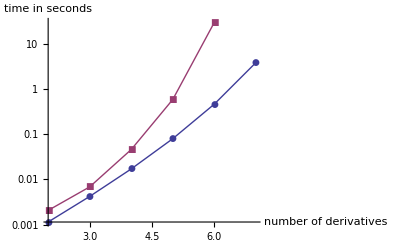

## Properties of symmetrized derivatives

Below we list some useful formulas and properties of symmetrized derivatives.

### Symmetrizing

Because it is always possible to commute adjacent covariant derivatives by introducing curvature, a symmetrized covariant derivative can in general be expressed as

∇_(a_1... a_n) = ∇_a_1 ...∇_a_n + polynomial in curvature ,

or vice-versa:

∇_a_1 ... ∇_a_n=  ∇_(a_1... a_n) - polynomial in curvature .

For example, we have

∇_(ab) T^c= 1/2(∇_a ∇_b +∇_b ∇_a)T^c
		= 1/2(∇_a ∇_b +∇_a ∇_b +∇_b ∇_a -∇_a ∇_b)T^c
		= (∇_a ∇_b +1/2[∇_b,∇_a])T^c
		= ∇_a ∇_b T^c+1/2 R_abd^c T^d+1/2 T_ab^d∇_d T^c .

By induction, we can deduce that a single ordinary derivative can be eaten by a symmetrized derivative as follows:

∇_(a_1... a_n) ∇_b = ∇_(a_1... a_n b) -D[i/(n+1)]_(a_1... a_n, b) ,

∇_b ∇_(a_1... a_n) = ∇_(a_1... a_n b) -D[(n+1-i)/(n+1)]_(a_1... a_n, b) ,

where the general commutator operator D is given by

D[f(i)]_(a_1... a_n, b) = D[f(i)]_((a_1... a_n), b) = ∑_(i=1)^n f(i)∇_(a_1... a_(i-1)) [∇_b,∇_a_i] ∇_(a_(i+1)... a_n) .

Although it is not explicitly indicated after the last equal sign because it would clutter notation, all a indices above are symmetrized over.
This expression for the operator D is not completely closed; it contains terms of the form

∇_(a_1... a_n) ∇_(b_1... b_m)

for which it is quite hard to find a closed formula relating it to ∇_(a_1... a_n b_1... b_m) .
However, whenever there is no torsion, the operator D can be expressed as

D[f(i)]_(a_1... a_n, b) = ∑_(i=0)^(n-1) g_1(i,n) (∇_(a_1... a_i) [∇_b,∇_(a_(i+1))])∇_(a_(i+2)... a_n) 
		+ ∑_(i=0)^(n-2) g_2(i,n)(∇_(a_1... a_i) (R_(ba_(i+1)a_(i+2)))^c)∇_(a_(i+3)... a_n c) 
	-∑_(i=0)^(n-3) (∇_(a_1... a_i) (R_(ba_(i+1)a_(i+2)))^c)D[g_3(n,i)(j)]_(a_(i+3)... a_n, c)

where the commutator in the first term does not act on the indices of ∇_(a_(i+2)... a_n) , but only on the expression on which the operator D acts. Furthermore, the numeric functions g_i are given by

g_1(i,n)        = ∑_(k=i+1)^(n-1) f(k)(k-1
i)
	g_2(i,n)        = ∑_(k=i+1)^(n-1) f(k)(n-k)(k-1
i)
	g_3(n,i)(j) = ∑_(k=i+1)^(n-1) f(k)(n-k)(k-1
i)(j/(n-i-1)-Θ(i+j-k)(i+j-k+1)/(n-k))

where Θ is the UnitStep function. Note that g_3(n,i)(j) with fixed n and i gets fed into the next iteration of  D as its f (j).
A similar closed form for D with torsion should also exist.

### Other properties

Distributivity is inherited from the ordinary derivative:

∇_(a_1... a_n) (X+Y)= ∇_(a_1... a_n) X+∇_(a_1... a_n) Y .

If the ordinary derivative is Leibnitz, we have the following generalization of the Leibnitz rule:

∇_(a_1... a_n) (X Y)= ∑_(i=0)^n (n
i)∇_((a_1... a_i) X  ∇_(a_(i+1)... a_n)) Y .

A consistency check on this formula is counting the number of terms on boths sides; the left-hand-side has 2^n terms, the same as the right-hand-side, namely ∑_(i=0)^n (n
i)=2^n.

Integrating by parts also carries over nicely:

Y ∇_(a_1... a_n) X=(-1)^n  X ∇_(a_1... a_n) Y+ total derivative.

Lastly, the action of a Leibnitz symmetrized derivative on a generic function F with arguments  X^μ (μ = 1,…,p)  can be written as the following generalized chain rule:

∇_(a_1⋯ a_n) F(X^μ) = ∑_(i=1)^n (∂_μ_1 ⋯∂_μ_i F(X^μ)∑_({k_1,…, k_i}∈P(n,i)) M(k_1,…,k_i) ∇_((a_1... a_k_1) X^μ_1⋯∇_(a_(n-k_i+1)⋯ a_n)) X^μ_i).

Here ∂_μ = ∂/(∂X^μ) , and the contracted μ indices are summed over. Furthermore, P(n,i) denotes the set of partitions of n into i integers {k_1,…,k_i} (to be precise,  P(n,i) is the result of IntegerPartitions[n,{i}]). And M is the weighted multinomial

M(k_1,…,k_i)  = (Multinomial(k_1,…,k_i))/(∏_(p=1)^n Count({k_1,…,k_i},p)!).

Note that

∑_({k_1,…, k_i}∈P(n,i)) M(k_1,…,k_i)  = 𝒮_n^(i),            ∑_(i=1)^n 𝒮_n^(i)= B_n,

where  𝒮_n^(i) is the Stirling number of the second kind, and B_n is the Bell number.

The generalized Leibnitz rule above is actually a limiting case of the generalized chain rule, as we can see by setting F(X^μ) = X Y:

∇_(a_1⋯ a_n) (X Y) = ∂_X (X Y)M(n) ∇_(a_1... a_n) X  + ∂_Y (X Y)M(n) ∇_(a_1... a_n) Y 
			 + ∂_X ∂_Y (X Y)∑_(k=1)^⌊n/2⌋ M(k,n-k)∇_((a_1... a_k) X∇_(a_(k+1)⋯ a_n)) Y
			 + ∂_Y ∂_X (X Y)∑_(k=1)^⌊n/2⌋ M(k,n-k)∇_((a_1... a_k) Y∇_(a_(k+1)⋯ a_n)) X
			=  Y ∇_(a_1... a_n) X  + X ∇_(a_1... a_n) Y + ∑_(k=1)^(n-1) (n
k)∇_((a_1... a_k) X∇_(a_(k+1)⋯ a_n)) Y
			=∑_(k=0)^n (n
k)∇_((a_1... a_k) X∇_(a_(k+1)⋯ a_n)) Y .

Similarly, the distributivity property is also a limiting case of the generalized chain rule.

More About

Related Tutorials

Related Wolfram Education Group Courses